## Manipulate the Bode Plot (Working)

```mathematica
XVF
```

{X1→(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4),X2→(F1 (0.0000122042+3.375×10^-6 s+2.33333×10^-7 s^2)+F2 (0.0000244085+6.75×10^-6 s+0.0000245738 s^2+3.33333×10^-6 s^3))/(1.23568+0.512578 s+9.83427 s^2+2.70327 s^3+7.41881 s^4+1. s^5)}

```mathematica
XVF[[1,1,2]]
```

(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4)

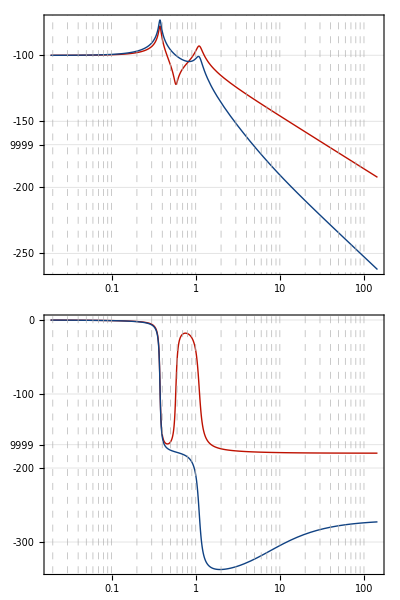

```mathematica
BodePlot[{XVF[[1,1,2]]/.{F1->1,F2->0},XVF[[1,1,2]]/.{F1->0,F2->1}},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed]]
```

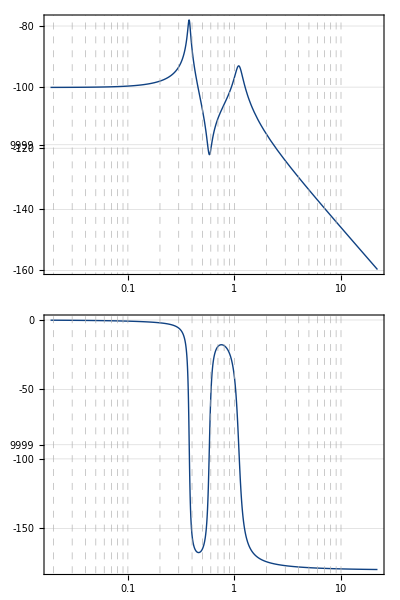

```mathematica
BodePlot[XVF[[1,1,2]]/.{F1->1,F2->0},ImageSize->550,Frame->True,PlotStyle->{Directive[Thick,ColorData[20,1]],Directive[Thick,ColorData[20,9]]},Frame->False,AspectRatio->1/2.25,GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.7],Dashed]]
```

```mathematica
XVF[[1,1,2]]/.{s->ⅉ ω}
```

(F2 (1.6875×10^-6+(0.+2.33333×10^-7 ⅈ) ω)+F1 (1.6875×10^-6+(0.+2.33333×10^-7 ⅈ) ω-5.×10^-6 ω^2))/(0.170859+(0.+0.04725 ⅈ) ω-1.35327 ω^2-(0.+0.186667 ⅈ) ω^3+1. ω^4)

### Let’s investigate the influence of the two forces on the displacement of the first floor of the building.

```mathematica
Manipulate[Plot[
20*Log[(F2 (1.6875*10^-6+(0.+2.33333*10^-7 I) ω)+F1 (1.6875*10^-6+(0.+2.33333*10^-7 I) ω-5.*10^-6 ω^2))/(0.170859+(0.+0.04725 I) ω-1.35327 ω^2-(0.+0.186667 I) ω^3+1. ω^4)],
{ω,0,100}],
{F1,0,1},{F2,0,1}]
```